```mathematica
Solve[Sin[x]+2*Cos[4*x]==√3*Cos[x],x,Ima]
```

{{x→ConditionalExpression[-(5 π)/6+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[π+ArcTan[(-4 (-1)^(8/9)-(8 ⅈ)/(1/2 (ⅈ-√3))^(1/3)+(6 √3)/(1/2 (ⅈ-√3))^(1/3)-ⅈ 2^(2/3) (ⅈ-√3)^(1/3)+8 2^(1/3) (ⅈ-√3)^(2/3))/(2 (-1/(1/2 (ⅈ-√3))^(1/3)-(1/2 (ⅈ-√3))^(1/3)))]+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[ArcTan[(4+4 √5+√6 (5-√5)^(3/2)+√30 (5-√5)^(3/2)+4 √(6 (5-√5))-4 √(30 (5-√5)))/(4 (√3+√15-√(2 (5-√5))))]+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[ArcTan[(4+4 √5-√6 (5-√5)^(3/2)-√30 (5-√5)^(3/2)-4 √(6 (5-√5))+4 √(30 (5-√5)))/(4 (√3+√15+√(2 (5-√5))))]+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[ArcTan[(4-4 √5-√6 (5+√5)^(3/2)+√30 (5+√5)^(3/2)-4 √(6 (5+√5))-4 √(30 (5+√5)))/(4 (√3-√15+√(2 (5+√5))))]+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[π+ArcTan[(4-4 √5+√6 (5+√5)^(3/2)-√30 (5+√5)^(3/2)+4 √(6 (5+√5))+4 √(30 (5+√5)))/(4 (√3-√15-√(2 (5+√5))))]+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[-π+ArcTan[(-2+√3 ((1-ⅈ √3)/(2 2^(2/3) (ⅈ-√3)^(1/3))+1/4 (1/2 (ⅈ-√3))^(1/3) (1+ⅈ √3))+16 ((1-ⅈ √3)/(2 2^(2/3) (ⅈ-√3)^(1/3))+1/4 (1/2 (ⅈ-√3))^(1/3) (1+ⅈ √3))^2-16 ((1-ⅈ √3)/(2 2^(2/3) (ⅈ-√3)^(1/3))+1/4 (1/2 (ⅈ-√3))^(1/3) (1+ⅈ √3))^4)/((1-ⅈ √3)/(2 2^(2/3) (ⅈ-√3)^(1/3))+1/4 (1/2 (ⅈ-√3))^(1/3) (1+ⅈ √3))]+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[ArcTan[(-2+√3 (1/4 (1/2 (ⅈ-√3))^(1/3) (1-ⅈ √3)+(1+ⅈ √3)/(2 2^(2/3) (ⅈ-√3)^(1/3)))+16 (1/4 (1/2 (ⅈ-√3))^(1/3) (1-ⅈ √3)+(1+ⅈ √3)/(2 2^(2/3) (ⅈ-√3)^(1/3)))^2-16 (1/4 (1/2 (ⅈ-√3))^(1/3) (1-ⅈ √3)+(1+ⅈ √3)/(2 2^(2/3) (ⅈ-√3)^(1/3)))^4)/(1/4 (1/2 (ⅈ-√3))^(1/3) (1-ⅈ √3)+(1+ⅈ √3)/(2 2^(2/3) (ⅈ-√3)^(1/3)))]+2 π C[1],C[1]∈ℤ]}}

```mathematica
TrigReduce[Sin[x]+2*Cos[4*x]-√3*Cos[x]]
```

-√3 Cos[x]+2 Cos[4 x]+Sin[x]

```mathematica
TrigToExp[-√3 Cos[x]+2 Cos[4 x]+Sin[x]]
```

1/2 ⅈ ⅇ^(-ⅈ x)-1/2 √3 ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)-1/2 √3 ⅇ^(ⅈ x)+ⅇ^(-4 ⅈ x)+ⅇ^(4 ⅈ x)

```mathematica
Simplify[1/2 ⅈ ⅇ^(-ⅈ x)-1/2 √3 ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)-1/2 √3 ⅇ^(ⅈ x)+ⅇ^(-4 ⅈ x)+ⅇ^(4 ⅈ x)]
```

-1/2 (-ⅈ+√3) ⅇ^(-ⅈ x)-1/2 (ⅈ+√3) ⅇ^(ⅈ x)+ⅇ^(-4 ⅈ x)+ⅇ^(4 ⅈ x)

```mathematica
Solve[%==0,Reals]
```

{{x→ConditionalExpression[-(5 π)/6+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[2 ArcTan[Root[1-12 #1+3 #1^2+40 #1^3+3 #1^4-12 #1^5+#1^6&,1]]+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[2 ArcTan[Root[1-12 #1+3 #1^2+40 #1^3+3 #1^4-12 #1^5+#1^6&,3]]+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[2 ArcTan[Root[1-12 #1+3 #1^2+40 #1^3+3 #1^4-12 #1^5+#1^6&,5]]+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[2 ArcTan[Root[1+16 #1-60 #1^2-16 #1^3+134 #1^4-16 #1^5-60 #1^6+16 #1^7+#1^8&,3]]+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[2 ArcTan[Root[1+16 #1-60 #1^2-16 #1^3+134 #1^4-16 #1^5-60 #1^6+16 #1^7+#1^8&,4]]+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[2 ArcTan[Root[1+16 #1-60 #1^2-16 #1^3+134 #1^4-16 #1^5-60 #1^6+16 #1^7+#1^8&,6]]+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[2 ArcTan[Root[1+16 #1-60 #1^2-16 #1^3+134 #1^4-16 #1^5-60 #1^6+16 #1^7+#1^8&,8]]+2 π C[1],C[1]∈ℤ]}}

```mathematica
First[%5]
```

{x→ConditionalExpression[ⅈ (-(ⅈ π)/18+2 ⅈ π C[1]),C[1]∈ℤ]}

```mathematica
FunctionPeriod[Sin[x]+2*Cos[4*x]-√3*Cos[x],x]
```

2 π

```mathematica
D[Log[u],u]
```

1/u

```mathematica
f[x_]:=Sin[x]/Cos[x]^2+Log[(1+Sin[x])/Cos[x]]
```

```mathematica
f'[x]
```

Sec[x]^3+Sec[x] Tan[x]^2+(Cos[x] (1+Sec[x] (1+Sin[x]) Tan[x]))/(1+Sin[x])

```mathematica
Simplify[Sec[x]^3+Sec[x] Tan[x]^2+(Cos[x] (1+Sec[x] (1+Sin[x]) Tan[x]))/(1+Sin[x])]
```

(2 Sec[x]^2 (Sec[x]+Tan[x]))/(1+Sin[x])

```mathematica
TrigReduce[(2 Sec[x]^2 (Sec[x]+Tan[x]))/(1+Sin[x])]
```

(8 (Sec[x]+Tan[x]))/(2+2 Cos[2 x]+Sin[x]+Sin[3 x])

```mathematica
Reduce[(2 Sec[x]^2 (Sec[x]+Tan[x]))/(1+Sin[x])]
```

Reduce::naqs: (2 Sec[x]^2 (Sec[x]+Tan[x]))/(1+Sin[x]) is not a quantified system of equations and inequalities.

Reduce[(2 Sec[x]^2 (Sec[x]+Tan[x]))/(1+Sin[x])]

```mathematica
(2 Sec[x]^2 (Sec[x]+Tan[x]))/(1+Sin[x])===2/Cos[x]^3
```

False

```mathematica
TrueQ[(2 Sec[x]^2 (Sec[x]+Tan[x]))/(1+Sin[x])==2/Cos[x]^3]
```

False

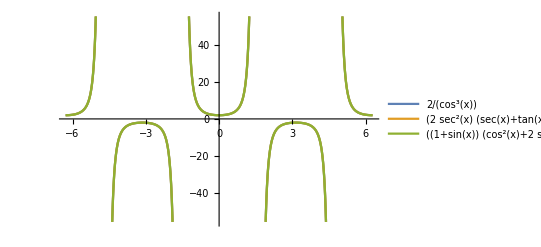

```mathematica
Plot[{2/Cos[x]^3,(2 Sec[x]^2 (Sec[x]+Tan[x]))/(1+Sin[x]),((1+Sin[x])(Cos[x]^2+2*Sin[x]^2)+Cos[x]^2(Cos[x]^2+(1+Sin[x])*Sin[x]))/(Cos[x]^3(1+Sin[x]))},{x,-2 Pi,2 Pi},PlotLegends->"Expressions"]
```